Make a slope field for y’ = sin[x]/x then plot taylor solutions....

1.-0.166667 x^2+0.00833333 x^4

1.-0.166667 x^2+0.00833333 x^4-0.000198413 x^6+2.75573×10^-6 x^8-2.50521×10^-8 x^10

1.-0.166667 x^2+0.00833333 x^4-0.000198413 x^6+2.75573×10^-6 x^8-2.50521×10^-8 x^10+1.6059×10^-10 x^12-7.64716×10^-13 x^14

1.-0.166667 x^2+0.00833333 x^4-0.000198413 x^6+2.75573×10^-6 x^8-2.50521×10^-8 x^10+1.6059×10^-10 x^12-7.64716×10^-13 x^14+2.81146×10^-15 x^16-8.22064×10^-18 x^18+1.95729×10^-20 x^20

1.-0.166667 x^2+0.00833333 x^4-0.000198413 x^6+2.75573×10^-6 x^8-2.50521×10^-8 x^10+1.6059×10^-10 x^12-7.64716×10^-13 x^14+2.81146×10^-15 x^16-8.22064×10^-18 x^18+1.95729×10^-20 x^20-3.86817×10^-23 x^22+6.44695×10^-26 x^24

1.-0.166667 x^2+0.00833333 x^4-0.000198413 x^6+2.75573×10^-6 x^8-2.50521×10^-8 x^10+1.6059×10^-10 x^12-7.64716×10^-13 x^14+2.81146×10^-15 x^16-8.22064×10^-18 x^18+1.95729×10^-20 x^20-3.86817×10^-23 x^22+6.44695×10^-26 x^24-9.18369×10^-29 x^26+1.131×10^-31 x^28-1.21613×10^-34 x^30+1.15163×10^-37 x^32-9.67759×10^-41 x^34

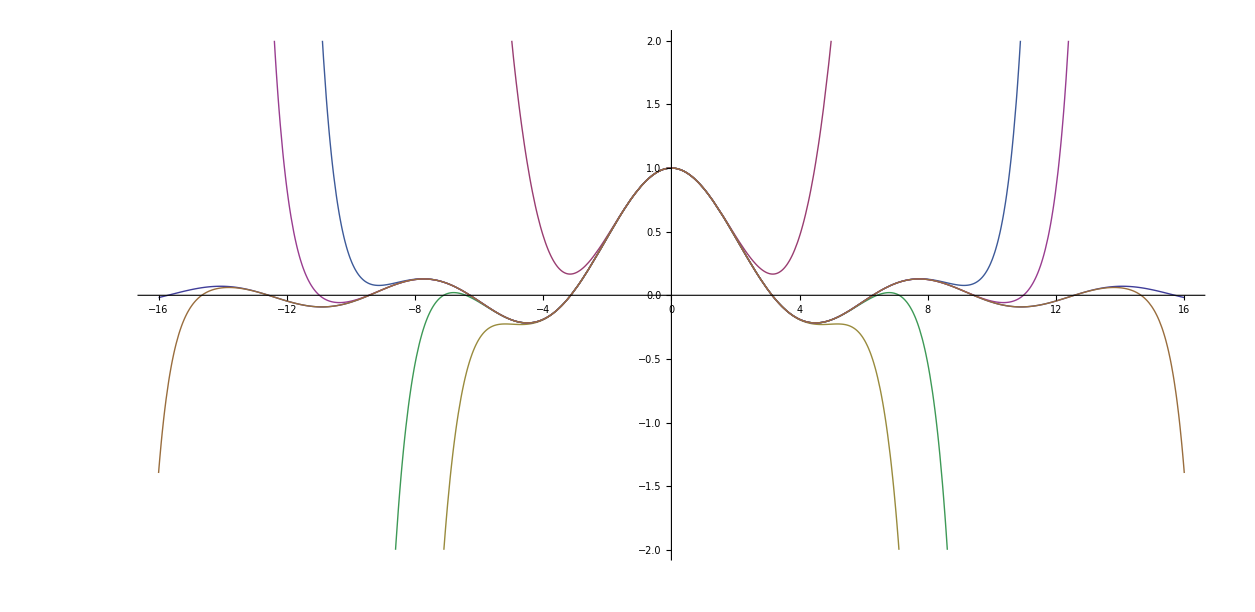

```mathematica
f1[x_]=Normal[Series[1.Sin[x]/x,{x,0,5}]]
f2[x_]=Normal[Series[1. Sin[x]/x,{x,0,10}]]
f3[x_]=Normal[Series[1.Sin[x]/x,{x,0,15}]]
f4[x_]=Normal[Series[1.Sin[x]/x,{x,0,20}]]
f5[x_]=Normal[Series[1.Sin[x]/x,{x,0,25}]]
f6[x_]=Normal[Series[1.Sin[x]/x,{x,0,35}]]
Plot[{Sin[x]/x,f1[x],f2[x],f3[x],f4[x],f5[x],f6[x]},{x,-16,16},PlotRange->{-2,2},AspectRatio->4/8.2,PlotStyle->Thick]
```